# Risk Plots

## Bellman solutions

Plots show a convex hull of the feasible set.  Some add traces of solutions for iid mean process (as in the iid spike-and-slab Bayesian model).

For each configuration run, the data that is read from C++ is structured as a list of 3 items
	file name
	parameter values (as alpha, beta, omega, scale and n)
	simulation results.
A nested list of parameter values is given for the row (oracle) and column (statistician) players, followed by the universal scale (which may not be relevant) and the length of the test sequence.  For each player, the list includes the initial wealth W_0, the probability parameter, and the payout ω.  The probability parameter identifies the alpha-investing method, as defined below.

Transfer file from server.  Parsing of parameter values, with special cases... 
	alpha = defines oracle		 					0 mins LS risk, and 1 mins risk, and other mins testimator risk
	beta = rate used by bidder if geometric				0 for universal (if omega=0, then bid = beta/n)
	omega = payout for each player					0 indicates fixed bid (ie, old fashioned), 1 means unconstrained
	scale = scale parameter of universal distribution

### Functions for plotting and reading data ...

Idea is to make a file name based on parameter values.  Keep the file name and list of parameter values as the first two items in a list with the data last.

```mathematica
Clear[fmt,makeID,  getAlpha, getBeta,getOmegaAlpha,getOmegaBeta, getW0Alpha, getW0Beta,getN, getData];

fmt[x_]:=With[{s= ToString[Round[100x]]},
If[StringLength[s]>1,s,StringJoin["0",s]]
]

makeID[{W0α_,α_,ωα_},{W0β_,β_,ωβ_}, scale_, n_] :=
{StringJoin["summary_risk",
"_alpha",fmt[W0α],"_",fmt[α],"_",fmt[ωα],
"_beta"  ,fmt[W0β],"_",fmt[β],"_",fmt[ωβ] ,
"_scale",ToString[scale],"_n",ToString[n]],
{{W0α,α,ωα},{W0β,β,ωβ},scale,n}
}

getAlpha[{_,parms_,_}] :=getAlpha[parms]
getAlpha[{{_,α_,_},_List,_,_}] :=α

getBeta[{_,parms_,_}] :=getBeta[parms]
getBeta[{_List,{_,β_,_},_,_}] :=β

getAlphaBeta[{_,parms_,_}] :=getAlphaBeta[parms]
getAlphaBeta[{{_,α_,_},{_,β_,_},_,_}] :={α,β}

getOmegaAlpha[{_,parms_,_}]:=getOmegaAlpha[parms]
getOmegaAlpha[{{_,_,ω_},_List,_,_}]:=ω

getOmegaBeta[{_,parms_,_}]:=getOmegaBeta[parms]
getOmegaBeta[{_List,{_,_,ω_},_,_}]:=ω

getW0Alpha[{_,parms_,_}]:=getW0Alpha[parms]
getW0Alpha[{{W0_,_,_},_List,_,_}]:=W0

getW0Beta[{_,parms_,_}]:=getW0Beta[parms]
getW0Beta[{_List,{W0_,_,_},_,_}]:=W0

getW0Omega[{_,parms_,_}] :=getW0Omega[parms]
getW0Omega[{_,{w0_,_,ω_},_,_}] :={w0,ω}

getN[{_,parms_,_}] :=getN[parms]
getN[{_List,_List,_,n_}] :=n


getData[{name_,parms_},figureNumber_,server_]:=Module[
{fN=ToString[figureNumber],
path=StringJoin["~/C/bellman/figures/f",ToString[figureNumber],"/"],
fullName,x, cmd},
fullName=StringJoin[path,name];
If[StringLength[server]>1,
cmd = StringJoin["scp ",server,fullName," ", path];
Run[cmd]];
x= Import[fullName, "Table"];
If[x===$Failed,
Print[name," read failed."];{name,parms,Null},
{name,parms,Sort[x,#1⟦1⟧<#2⟦1⟧&]} (* sort on angle *)
]]
```

The function pickColumns adds 1 to the risk (as for implicitly estimating a constant) to work with log/log plot.

```mathematica
Clear[pickColumns, playerName,drawFeasibleSet,drawLogFeasibleSet];

pickColumns[simres_] :=With[
{cols = Length[First[simres]]-{1,0}},
 1 +(#⟦cols⟧&)/@ simres
]

playerName[list_List] := playerName[list⟦1⟧,list⟦2⟧];
playerName[α_,0] := StringJoin["Bonferroni(",ToString[α],")"]
playerName[0,1] := "Least Squares";
playerName[1,1] := "RI Oracle"
playerName[α_,1] := StringJoin["Oracle(",ToString[α],")"]
playerName[α_,ω_] := StringJoin["Geom(",ToString[α],",",ToString[ω],")"]

drawFeasibleSet[{name_,{{W0α_,α_,ω1_},{W0β_,β_,ω2_},σ_,n_},simres_},{join_:False,color_:Blue}]:=Module[
{xy =pickColumns[simres]},
ListPlot[xy,
Joined->join,
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω2],")"],
BaseStyle->{Gray,Larger,FontFamily->"Chalkboard",FontSize->10},
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]

drawLogFeasibleSet[{name_,{{W0α_,α_,ω1_},{W0β_,β_,ω2_},σ_,n_},simres_},{join_:False,color_:Blue}] := Module[
{xy=pickColumns[simres]},
ListLogLogPlot[xy,
Print["2 log n =",2.Log[n]];
Joined->join,
PlotRange->{{1,1.2Max[xy]},{1,1.15Max[xy]}},
AspectRatio->1,
PlotStyle->{color,PointSize[0.015]},
AxesLabel->{playerName[α,ω1],playerName[β,ω2]},
PlotLabel->StringJoin["Feasible Risks  n=",ToString[n],", ω=",ToString[ω2],")"],
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->10}, 
Epilog->{ (* LogLogPlot exponentiates all before drawing, as if these are on log scale *)
Orange,Line[{{0.01,0.01},{100,100}}],
Red, Line[{{0,Log[1+2Log[n]]},{Log[20000],Log[20000+20000(2Log [n])]}}],
color,(*Arrow[Log[xy]]*)}]
]
```

```mathematica
Clear[drawFeasibleSets,drawLogFeasibleSets, drawSets];

drawFeasibleSets[simres_List,{label_,getCmd_},opts:OptionsPattern[]]:=
drawSets[ListPlot,simres,{label,getCmd},opts]

drawLogFeasibleSets[simres_List, {label_,getCmd_},opts:OptionsPattern[]]:=
drawSets[ListLogLogPlot,simres, {label,getCmd},opts]

drawSets[f_,simres_List,{label_,getCmd_},opts:OptionsPattern[]]:=Module[
{xy =(pickColumns[#⟦3⟧]&)/@simres,
legend=ToString/@getCmd/@simres
},
f[xy,
AspectRatio->1,opts,
BaseStyle->{Black,Larger,FontFamily->"Chalkboard",FontSize->12},
PlotLegends->SwatchLegend[legend, LegendLabel-> label],
Epilog->{Orange,Line[{{0.0,0.0},{1000,1000}}] }
]
]
```

### Figure 1 Feasible risks for geometric bidder with varying W_0 and ω_β, with RI oracle

Idea is to show that you want to have a larger payout than might have been expected from usual testing. These first runs vary the initial wealth and payout for a Geometric bidder that spends 1% on the next round.

```mathematica
id = With[
{α=1,ωα=1,W0α=1,β=0.01,scale=2,n=500},
Join[ (* 3 sets of 5 each *)
makeID[{W0α,α,ωα},{   #   ,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (* Subscript[W, 0]=ω *)
makeID[{W0α,α,ωα},{0.05,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (*Subscript[W, 0]=0.05*)
makeID[{W0α,α,ωα},{0.50,β,#},scale,n]&/@ {0.05,0.10,0.25,0.50,0.75}     (*Subscript[W, 0]=0.50*)
]]

f1Data=Table[getData[id⟦i⟧,1,"variance:"],{i,1,Length[id]}];
```

{{summary_risk_alpha100_100_100_beta05_01_05_scale2_n500,{{1,1,1},{0.05,0.01,0.05},2,500}},{summary_risk_alpha100_100_100_beta10_01_10_scale2_n500,{{1,1,1},{0.1,0.01,0.1},2,500}},{summary_risk_alpha100_100_100_beta25_01_25_scale2_n500,{{1,1,1},{0.25,0.01,0.25},2,500}},{summary_risk_alpha100_100_100_beta50_01_50_scale2_n500,{{1,1,1},{0.5,0.01,0.5},2,500}},{summary_risk_alpha100_100_100_beta75_01_75_scale2_n500,{{1,1,1},{0.75,0.01,0.75},2,500}},{summary_risk_alpha100_100_100_beta05_01_05_scale2_n500,{{1,1,1},{0.05,0.01,0.05},2,500}},{summary_risk_alpha100_100_100_beta05_01_10_scale2_n500,{{1,1,1},{0.05,0.01,0.1},2,500}},{summary_risk_alpha100_100_100_beta05_01_25_scale2_n500,{{1,1,1},{0.05,0.01,0.25},2,500}},{summary_risk_alpha100_100_100_beta05_01_50_scale2_n500,{{1,1,1},{0.05,0.01,0.5},2,500}},{summary_risk_alpha100_100_100_beta05_01_75_scale2_n500,{{1,1,1},{0.05,0.01,0.75},2,500}},{summary_risk_alpha100_100_100_beta50_01_05_scale2_n500,{{1,1,1},{0.5,0.01,0.05},2,500}},{summary_risk_alpha100_100_100_beta50_01_10_scale2_n500,{{1,1,1},{0.5,0.01,0.1},2,500}},{summary_risk_alpha100_100_100_beta50_01_25_scale2_n500,{{1,1,1},{0.5,0.01,0.25},2,500}},{summary_risk_alpha100_100_100_beta50_01_50_scale2_n500,{{1,1,1},{0.5,0.01,0.5},2,500}},{summary_risk_alpha100_100_100_beta50_01_75_scale2_n500,{{1,1,1},{0.5,0.01,0.75},2,500}}}

Examine results for a run to see where convex set is very flat around 90-95 degrees (n=500).

```mathematica
f1Data[[4,3]]//TableForm
```

This version shows the convex hull when W_0=ω.

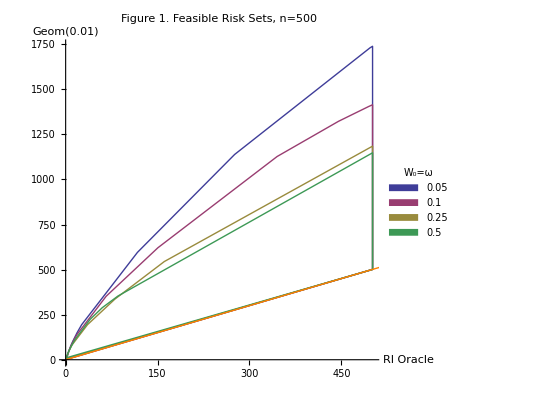

```mathematica
figure1=With[{β=ToString[getBeta[f1Data⟦1⟧]]}, (* Common geometric spending rate *)
drawFeasibleSets[
f1Data⟦{1,2,3,4}⟧, (* omit the ω=0.75 to keep simple *)
{"W_0=ω",getOmegaBeta},
PlotLabel->"Figure 1. Feasible Risk Sets, n=500",
AxesLabel ->{"RI Oracle",StringJoin["Geom(",β,")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]
```

Comments on log scale plot:
	Log version for small risks; add one to everything to be logable.  
	Add 1 as in the F&G paper for the forced estimation of an intercept. 
	Feasible set is not convex in this new coordinate system...

```mathematica
colors=GrayLevel /@ {0.2,0.3,0.4,0.6,0.8};
f1LogPlots=Table[drawLogFeasibleSet[f1Data⟦i⟧,{False,colors⟦i⟧}],{i,1,5}];
```

2 log n =12.4292

2 log n =12.4292

2 log n =12.4292

«2 more identical outputs»

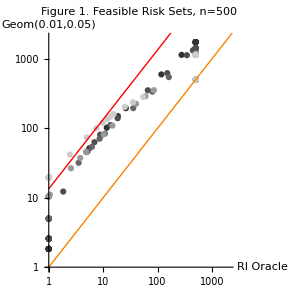

```mathematica
Show[f1LogPlots,PlotLabel->"Figure 1. Feasible Risk Sets, n=500"]
```

Now fix initial wealth W_0 while allowing ω to vary.  

For (a), the geometric bidder does not get much to start, but can get large payout. 
For (b), it starts with a lot but payout may be small.

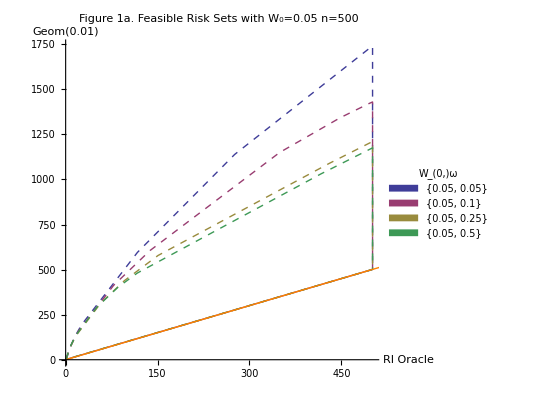

```mathematica
figure1a=With[{
β=ToString[getBeta[f1Data⟦1⟧]],
W0=ToString[getW0Beta[f1Data⟦6⟧]]},
drawFeasibleSets[
f1Data⟦{6,7,8,9}⟧, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1a. Feasible Risk Sets with W_0=",W0," n=500"],
AxesLabel ->{"RI Oracle",StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashed,#}&/@ColorData[1,"ColorList"]],  Joined->True
]
]
```

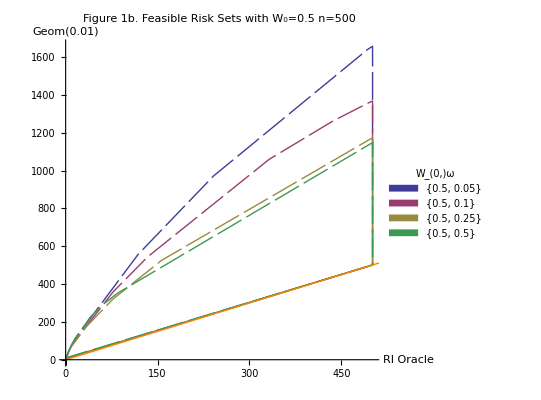

```mathematica
figure1b=With[{
β=ToString[getBeta[f1Data⟦1⟧]],
W0=ToString[getW0Beta[f1Data⟦11⟧]]},
drawFeasibleSets[
f1Data⟦{11,12,13,14}⟧, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1b. Feasible Risk Sets with W_0=",W0," n=500"],
AxesLabel ->{"RI Oracle",StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashing[{0.05,0.01}],#}&/@ColorData[1,"ColorList"]], 
Joined->True
]
]
```

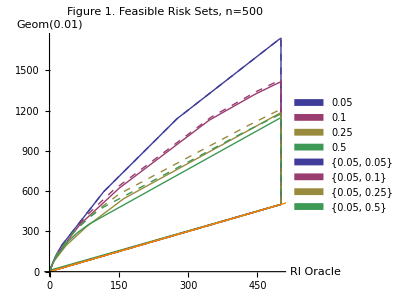

```mathematica
Show[figure1,figure1a, AxesLabel->{"RI Oracle", "Geom(0.01)"}]
```

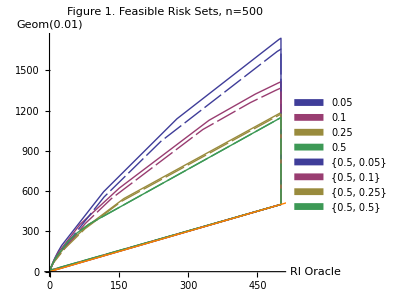

```mathematica
Show[figure1,figure1b]
```

#### Initial wealth effects ...

```mathematica
f1Data[[3,2]]
```

{{1,1,1},{0.5,0.1,0.5},2,500}

```mathematica
f1Data[[7,2]]
```

{{1,1,1},{0.05,0.1,0.5},2,500}

```mathematica
getcol[x_,j_]:= #⟦j⟧&/@x
```

```mathematica
Transpose[Join[Transpose[getcol[f1Data[[3,3]],{3,4,5,6,7,8}]]
,Transpose[getcol[f1Data[[7,3]],{4,8}]]]]//TableForm
```

0 | 0.5 | 500 | -7.18331 | 0 | -7.18331 | 0.5 | -1.90489
15 | 0.5 | 500 | -6.93855 | 0 | -7.18331 | 0.5 | -1.90489
30 | 0.5 | 500 | -6.22093 | 0 | -7.18331 | 0.5 | -1.90489
45 | 0.5 | 500 | -5.07937 | 0 | -7.18331 | 0.5 | -1.90489
60 | 0.5 | 500 | -3.59166 | 0 | -7.18331 | 0.5 | -1.90489
65 | 0.5 | 500 | -3.0358 | 0 | -7.18331 | 0.5 | -1.90489
70 | 0.5 | 500 | -2.45684 | 0 | -7.18331 | 0.5 | -1.90489
75 | 0.5 | 500 | -1.85918 | 0 | -7.18331 | 0.5 | -1.90489
80 | 0.5 | 500 | -1.24737 | 0 | -7.18331 | 0.5 | -1.90489
85 | 0.5 | 500 | -0.626067 | 0 | -7.18331 | 0.5 | -1.90489
90 | 0.5 | 500 | 3.6661×10^-11 | 0 | -7.18331 | 0.5 | -1.90489
91 | 0.5 | 500 | 0.125366 | 0 | -7.18331 | 0.5 | -1.90489
92 | 0.5 | 500 | 0.250694 | 0 | -7.18331 | 0.5 | -1.90489
93 | 0.5 | 500 | 0.375946 | 0 | -7.18331 | 0.5 | -1.90489
93.2 | 0.5 | 500 | 0.400984 | 0 | -7.18331 | 0.5 | -1.90489
93.4 | 0.5 | 500 | 0.426016 | 0 | -7.18331 | 0.5 | -1.90489
93.6 | 0.5 | 500 | 0.451044 | 0 | -7.18331 | 0.5 | -1.90489
93.8 | 0.5 | 500 | 0.476067 | 0 | -7.18331 | 0.5 | -1.90489
94 | 0.5 | 500 | 0.501083 | 0 | -7.18331 | 0.5 | -1.90489
94.2 | 0.5 | 500 | 0.526093 | 0 | -7.18331 | 0.5 | -1.90489
94.4 | 0.5 | 500 | 0.551097 | 0 | -7.18331 | 0.5 | -1.90489
94.6 | 0.5 | 500 | 0.576094 | 0 | -7.18331 | 0.5 | -1.90489
94.8 | 0.5 | 500 | 0.601085 | 0 | -7.18331 | 0.5 | -1.90489
95 | 0.5 | 500 | 0.626067 | 0 | -7.18331 | 0.5 | -1.90489
95.2 | 0.5 | 500 | 0.752366 | -10.7728 | -126.675 | 0.5 | -130.157
95.4 | 0.5 | 500 | 1.22536 | -12.0921 | -140.941 | 0.5 | -144.805
95.6 | 0.5 | 500 | 1.71763 | -12.6877 | -147.001 | 0.5 | -150.995
95.8 | 0.5 | 500 | 2.31029 | -14.0084 | -160.772 | 0.5 | -165.593
96 | 0.5 | 500 | 3.00357 | -15.7059 | -178.166 | 0.5 | -184.095
96.2 | 0.5 | 500 | 3.64537 | -16.5818 | -186.392 | 0.5 | -192.752
96.4 | 0.5 | 500 | 4.31301 | -17.4808 | -194.537 | 0.5 | -201.33
96.6 | 0.5 | 500 | 5.00828 | -18.3762 | -202.395 | 0.5 | -209.622
96.8 | 0.5 | 500 | 5.73082 | -19.2632 | -209.947 | 0.5 | -217.609
97 | 0.5 | 500 | 6.47853 | -20.0944 | -216.815 | 0.5 | -224.919
98 | 0.5 | 500 | 10.5188 | -24.5458 | -250.233 | 0.5 | -260.309
99 | 0.5 | 500 | 15.3458 | -30.1737 | -288.606 | 0.5 | -300.958
100 | 0.5 | 500 | 20.6994 | -35.7738 | -322.086 | 0.5 | -336.439
105 | 0.5 | 500 | 55.3742 | -66.3424 | -461.543 | 0.5 | -484.568
110 | 0.5 | 500 | 100.184 | -96.2019 | -557.23 | 0.5 | -586.156
115 | 0.5 | 500 | 153.278 | -128.996 | -639.321 | 0.5 | -673.327
120 | 0.5 | 500 | 210.176 | -150.771 | -681.495 | 0.5 | -718.069
125 | 0.5 | 500 | 270.226 | -174.91 | -720.922 | 0.5 | -759.882
135 | 0.5 | 500 | 391.67 | -211.954 | -765.856 | 0.5 | -807.519
150 | 0.5 | 500 | 564.512 | -256.864 | -800.145 | 0.5 | -843.64
165 | 0.5 | 500 | 712.561 | -300.062 | -818.099 | 0.5 | -862.534
180 | 0.5 | 500 | 820.883 | -327.311 | -820.883 | 0.5 | -865.44
195 | 0.5 | 500 | 880.188 | -346.686 | -818.344 | 0.5 | -862.808
210 | 0.5 | 500 | 884.085 | -369.455 | -807.55 | 0.5 | -851.666
225 | 0.5 | 500 | 837.915 | -412.344 | -772.647 | 0.5 | -818.426
240 | 0.5 | 500 | 762.088 | -493.942 | -668.643 | 0.5 | -736.592
255 | 0.5 | 500 | 653.037 | -499.999 | -657.124 | 0.5 | -728.258
270 | 0.5 | 500 | 500 | -500 | -500.036 | 0.5 | -500.035
285 | 0.5 | 500 | 353.552 | -500 | -500 | 0.5 | -500
300 | 0.5 | 500 | 183.013 | -500 | -500 | 0.5 | -500
315 | 0.5 | 500 | -1.26286×10^-8 | -500 | -500 | 0.5 | -500
330 | 0.5 | 500 | -6.22087 | -0.00129951 | -7.18399 | 0.5 | -1.90557
345 | 0.5 | 500 | -6.93855 | -1.25446×10^-6 | -7.18332 | 0.5 | -1.90489
359 | 0.5 | 500 | -7.18222 | 0 | -7.18331 | 0.5 | -1.90489

#### Saved

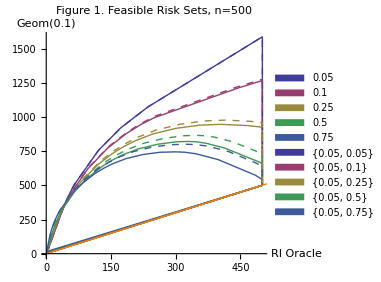
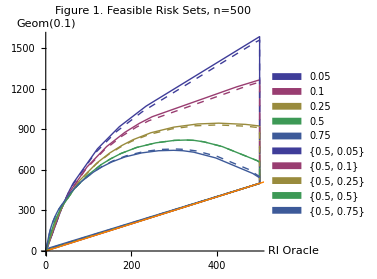

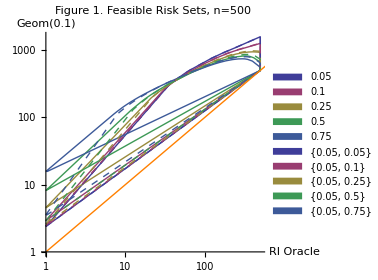
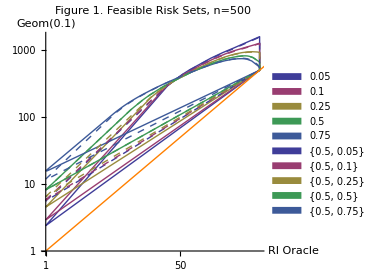

At a lower geometric spending rate β=0.01, the plot is more congested (all lose for high signal), but you really see problems with the high value for ω=0.75 in the low signal case.  You don’t gain by having ω=0.75 with high signal (you’re spending too slowly) but get bashed for little signal.  Setting the initial value to 0.05 in that case helps, but only for a little while.

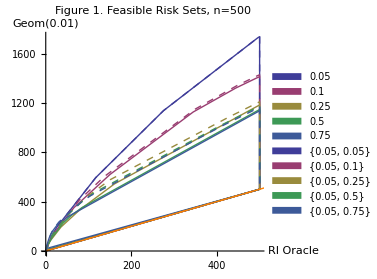
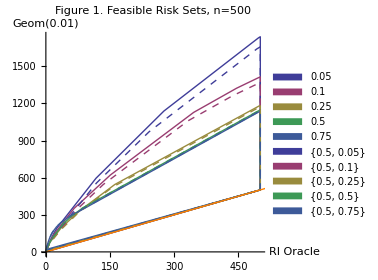

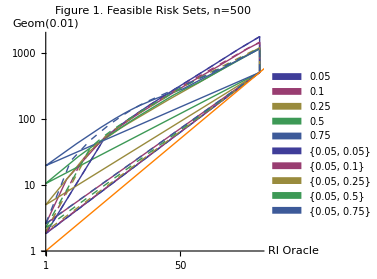
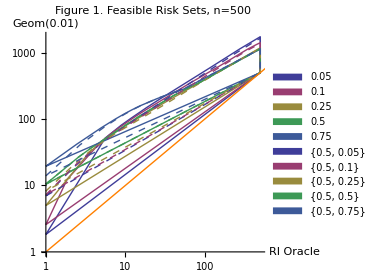

### Figure 2 Feasible risks for geometric bidder with varying W_0 and ω_β, with testimator oracle

Idea now is to reproduce the prior figures, but with a different oracle that is a fixed testimator (no wealth constraint, just a given testimator).

```mathematica
id = With[
{W0α=1,α=0.1,ωα=1,β=0.1,scale=2,n=500},
Join[ (* 3 sets of 5 each *)
makeID[{W0α,α,ωα},{   #   ,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (* Subscript[W, 0]=ω *)
makeID[{W0α,α,ωα},{0.05,β,#},scale,n]&/@ {0.05,0.10, 0.25,0.50,0.75} , (*Subscript[W, 0]=0.05*)
makeID[{W0α,α,ωα},{0.50,β,#},scale,n]&/@ {0.05,0.10,0.25,0.50,0.75}     (*Subscript[W, 0]=0.50*)
]]

f2Data=Table[getData[id⟦i⟧,1,""],{i,1,Length[id]}];
```

{{summary_risk_alpha100_10_100_beta05_10_05_scale2_n500,{{1,0.1,1},{0.05,0.1,0.05},2,500}},{summary_risk_alpha100_10_100_beta10_10_10_scale2_n500,{{1,0.1,1},{0.1,0.1,0.1},2,500}},{summary_risk_alpha100_10_100_beta25_10_25_scale2_n500,{{1,0.1,1},{0.25,0.1,0.25},2,500}},{summary_risk_alpha100_10_100_beta50_10_50_scale2_n500,{{1,0.1,1},{0.5,0.1,0.5},2,500}},{summary_risk_alpha100_10_100_beta75_10_75_scale2_n500,{{1,0.1,1},{0.75,0.1,0.75},2,500}},{summary_risk_alpha100_10_100_beta05_10_05_scale2_n500,{{1,0.1,1},{0.05,0.1,0.05},2,500}},{summary_risk_alpha100_10_100_beta05_10_10_scale2_n500,{{1,0.1,1},{0.05,0.1,0.1},2,500}},{summary_risk_alpha100_10_100_beta05_10_25_scale2_n500,{{1,0.1,1},{0.05,0.1,0.25},2,500}},{summary_risk_alpha100_10_100_beta05_10_50_scale2_n500,{{1,0.1,1},{0.05,0.1,0.5},2,500}},{summary_risk_alpha100_10_100_beta05_10_75_scale2_n500,{{1,0.1,1},{0.05,0.1,0.75},2,500}},{summary_risk_alpha100_10_100_beta50_10_05_scale2_n500,{{1,0.1,1},{0.5,0.1,0.05},2,500}},{summary_risk_alpha100_10_100_beta50_10_10_scale2_n500,{{1,0.1,1},{0.5,0.1,0.1},2,500}},{summary_risk_alpha100_10_100_beta50_10_25_scale2_n500,{{1,0.1,1},{0.5,0.1,0.25},2,500}},{summary_risk_alpha100_10_100_beta50_10_50_scale2_n500,{{1,0.1,1},{0.5,0.1,0.5},2,500}},{summary_risk_alpha100_10_100_beta50_10_75_scale2_n500,{{1,0.1,1},{0.5,0.1,0.75},2,500}}}

Look for the angle where risk increases suddenly.

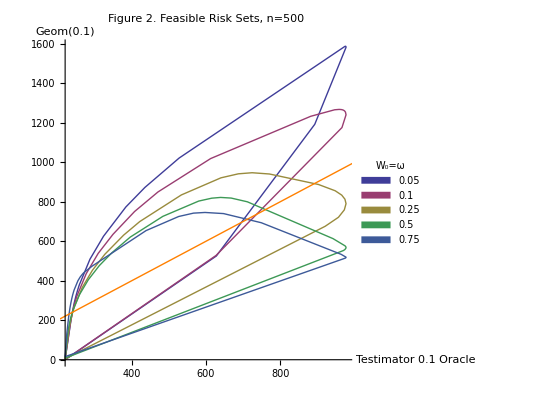

```mathematica
With[ {data=f2Data⟦{1,2,3,4,5}⟧},
figure2=With[
{α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]]}, (* Common geometric spending rate *)
drawFeasibleSets[
data, (* omit the ω=0.75 to keep simple *)
{"W_0=ω",getOmegaBeta},
PlotLabel->"Figure 2. Feasible Risk Sets, n=500",
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]]
```

Log scale is less interesting for these having seen them for the prior example.

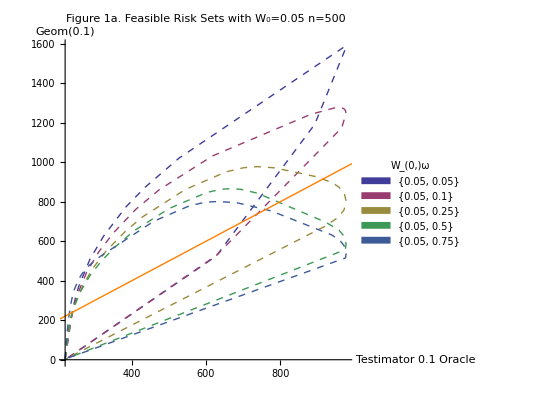

```mathematica
With[ {data=f2Data⟦{6,7,8,9,10}⟧},
figure2a=With[{
α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]],
W0=ToString[getW0Beta[data⟦1⟧]]},
drawFeasibleSets[
data, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 1a. Feasible Risk Sets with W_0=",W0," n=500"],
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashed,#}&/@ColorData[1,"ColorList"]],  Joined->True
]
]]
```

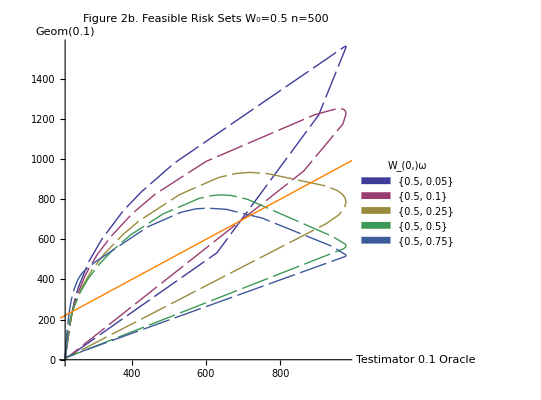

```mathematica
With[ {data=f2Data⟦{11,12,13,14,15}⟧},
figure2b=With[{
α=ToString[getAlpha[data⟦1⟧]],
β=ToString[getBeta[data⟦1⟧]],
W0=ToString[getW0Beta[data⟦1⟧]]},
drawFeasibleSets[
data, 
{"W_(0,)ω",getW0Omega},
PlotLabel->StringJoin["Figure 2b. Feasible Risk Sets  W_0=",W0," n=500"],
AxesLabel ->{StringJoin["Testimator ",α," Oracle"],StringJoin["Geom(",β,")"]},
PlotStyle-> Evaluate[{Dashing[{0.05,0.01}],#}&/@ColorData[1,"ColorList"]], 
Joined->True
]]]
```

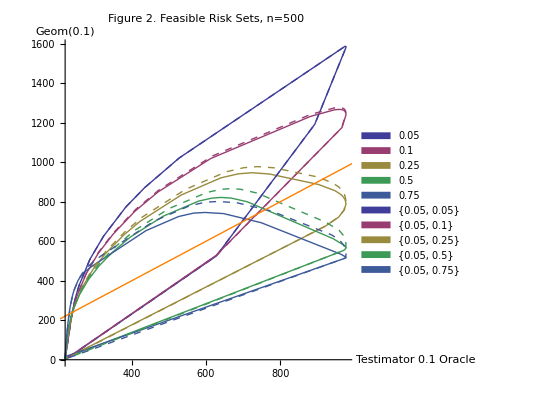

```mathematica
Show[figure2, figure2a]
```

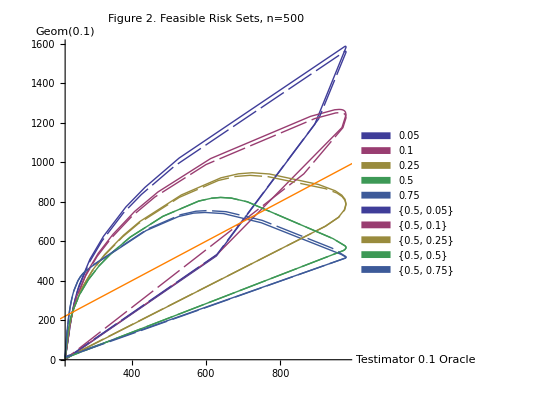

```mathematica
Show[figure2, figure2b]
```

### Figure 3 Paths within the feasible set, illustrating shape

This figure shows paths within the feasible set produced by non-zero means that occur with varying probabilities and varying sizes. The concave shape of the path within the feasible set shows that we are only gettin the convex boundary.  The figures require the data from figure 2 to show the boundary, then put these paths within that set.

```mathematica
stripCol[x_]:= #⟦{2,3}⟧&/@x

With[
{α=0.10,β=0.10,ω=0.5,scale=2,n=500},
With[
{path=StringJoin["~/C/bellman/figures/f3/risk_alpha",fmt[α],"_beta",fmt[β],"_omega",fmt[ω],"_scale",ToString[scale],"_n",ToString[n]]},
Print[StringJoin[path,"/m0.5"]];
rr[0.5]=-stripCol[Import[StringJoin[path,"/m0.5"], "Table"]];
rr[1.0]=-stripCol[Import[StringJoin[path,"/m1.0"], "Table"]];
rr[1.5]=-stripCol[Import[StringJoin[path,"/m1.5"], "Table"]];
rr[2.0]=-stripCol[Import[StringJoin[path,"/m2.0"], "Table"]];
rr[2.5]=-stripCol[Import[StringJoin[path,"/m2.5"], "Table"]];
rr[3.0]=-stripCol[Import[StringJoin[path,"/m3.0"], "Table"]];
rr[3.5]=-stripCol[Import[StringJoin[path,"/m3.5"], "Table"]];
rr[4.0]=-stripCol[Import[StringJoin[path,"/m4.0"], "Table"]];
]
]
```

~/C/bellman/figures/f3/risk_alpha10_beta10_omega50_scale2_n500/m0.5

Now add the data for the 2 - point distribution with pZero signal.  Take off the leading pZero column, leaving oracle and bidder risks.

```mathematica
With[
{μ={0.5,1.0,1.5,2.0,2.5,3.0,3.5,4.0}},
lp=ListPlot[rr/@μ,
PlotRange->All,
Joined->True,PlotLegends->SwatchLegend[μ,LegendLabel->"μ"],
PlotStyle->GrayLevel/@Range[0.9,0.1,-0.1]]
]
```

```mathematica
fp=drawFeasibleSet[f2Data⟦3⟧,{True,Blue}]
```

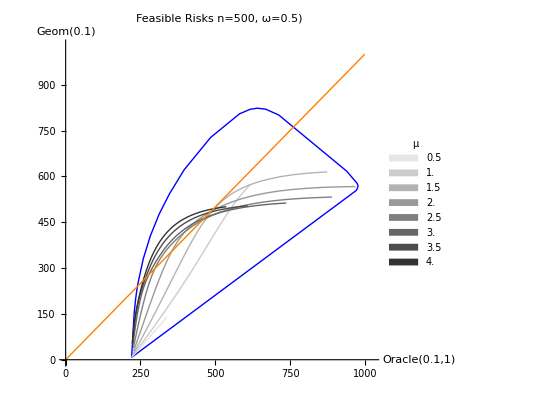

```mathematica
Show[fp,lp]
```

### Figure 4 Comparison of geometric bidders with different ω

```mathematica
id =With[
{α=0.1,ω1=0.05,β=0.1,ω2=0.50,scale=2,n=200},
{makeID[α        ,ω1,β        ,ω2,scale,n],
makeID[α/10,ω1,β        ,ω2,scale,n],
makeID[α/10,ω1,β/10,ω2,scale,n],
makeID[α         ,ω1,β/10,ω2,scale,n]}
]

f4Data=Table[getData[id⟦i⟧,4,""],{i,1,Length[id]}];
```

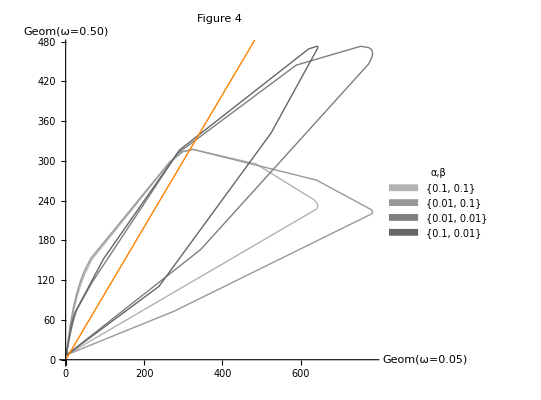

```mathematica
drawFeasibleSets[f4Data,"Figure 4",{"Geom(ω=0.05)","Geom(ω=0.50)"},{"α,β",getAlphaBeta}]
```

### Figure 5 Comparison of universal versus geometric bidders with different probabilities

```mathematica
id =With[
{α=0,W01=0.50,ω1=0.50,W02=0.5,ω2=0.50,scale=2,n=50},
makeID[{W01,α,ω1},{W02,#,ω2},scale,n]&/@{0.01,0.05,0.10}
]

f5Data=Table[getData[id⟦i⟧,5,""],{i,1,Length[id]}];
```

{{summary_risk_alpha50_00_50_beta50_01_50_scale2_n50,{{0.5,0,0.5},{0.5,0.01,0.5},2,50}},{summary_risk_alpha50_00_50_beta50_05_50_scale2_n50,{{0.5,0,0.5},{0.5,0.05,0.5},2,50}},{summary_risk_alpha50_00_50_beta50_10_50_scale2_n50,{{0.5,0,0.5},{0.5,0.1,0.5},2,50}}}

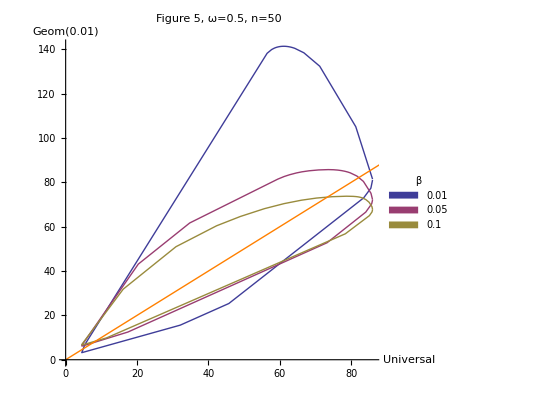

```mathematica
figure5=With[{β=ToString[getBeta[f5Data⟦1⟧]]},
drawFeasibleSets[
f5Data,
{"β",getBeta},
PlotLabel->"Figure 5, ω=0.5, n=50",
AxesLabel ->{"Universal",StringJoin["Geom(",β,")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]
```

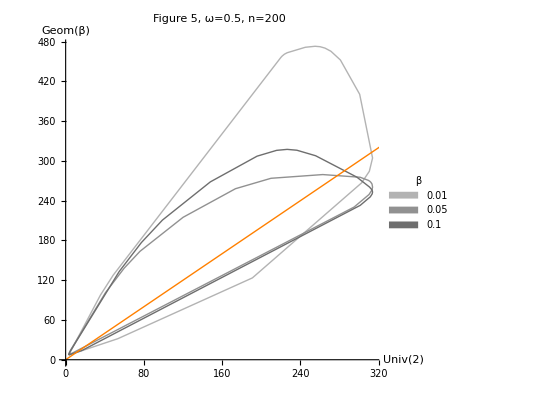

```mathematica
drawFeasibleSets[f5Data,"Figure 5, ω=0.5, n=200",
{f5Data⟦1,3,1,1⟧,"Geom(β)"},{β,getBeta}]
```

### Figure 6 Comparison of two testimators, unconstrained

Can do this one analytically since there is no state; keep constant wealth set by W_0.  Just maximize the comparitive risk.  

The figure here is more a way of aligning the C++ output to a simpler presentation arrangement, such as getting rid of the negative risk formulation and using a cosine/sine x-y pairing.  See the analysis in Risk.nb

```mathematica
figure = 6;
id = With[
{W0α=0.05,α=1,ωα=1,β=1,ωβ=1,scale=2,n=500},
makeID[{W0α,α,ωα},{# ,β,ωβ},scale,n]& /@ {0.10,0.15,0.20}
]

f6Data=Table[getData[id⟦i⟧,figure,""],{i,1,Length[id]}];
```

Examine results for a run to see where convex set is very flat around 90-95 degrees (n=500).

```mathematica
Take[f6Data⟦1,3⟧,30]//TableForm
```

This version shows the convex hull when W_0=ω.

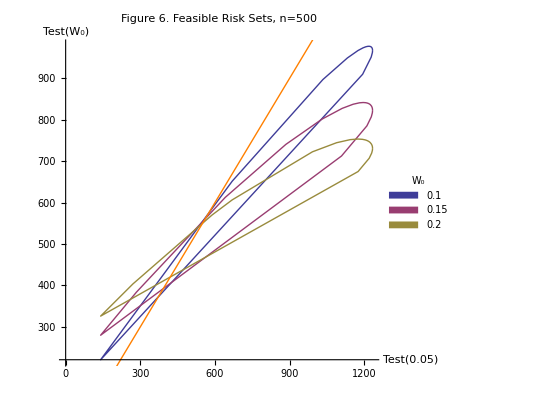

```mathematica
With[{data=f6Data},
figure6=With[{
α=ToString[getW0Alpha[data⟦1⟧]],
β=ToString[getW0Beta[data⟦1⟧]]
}, 
drawFeasibleSets[
data, (* omit the ω=0.75 to keep simple *)
{"W_0",getW0Beta},
PlotLabel->"Figure 6. Feasible Risk Sets, n=500",
AxesLabel ->{StringJoin["Test(",α,")"],StringJoin["Test(","W_0",")"]},
PlotStyle-> ColorData[1,"ColorList"],  Joined->True]
]]
```

### Additional Plots Risk Inflation, Effects of number of tests

This plot shows the feasible set in a log-log plot to zoom in on the growth trajectory.  Probably should not have that diagonal arrow returning to the left since the set is not convex on the log-log scale.

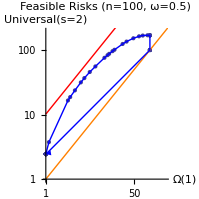
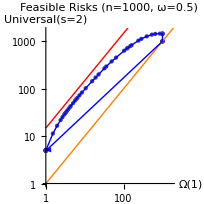
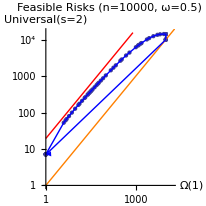
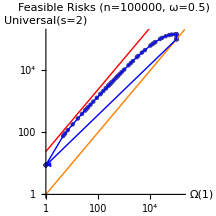

This is a plot to show the results for various values of n on the same graph. The align function rescales the oracle in the argument to match that in the reference set of coordinates.  Of course, all of the xy coordinate pairs (tables) need to be computed on the same grid.

```mathematica
(#⟦1⟧&/@xy[100])/(#⟦1⟧&/@xy[1000])xy[1000]
```

{{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1,4.97535},{1.,4.9781},{1.,7.46352},{1.,8.48179},{1.,9.09503},{1.,9.34627},{1.,9.54859},{1.,9.61351},{1.,9.6637},{1.,9.71541},{1.,9.76704},{1.,9.81115},{1.,9.83086},{1.,9.89444},{1.,9.92133},{1.,9.92079},{1.,9.91244},{1.,9.87986},{1.,9.81371},{1.14717,11.0705},{2.66802,24.7584},{2.94506,26.5979},{3.63303,31.9382},{4.72828,39.5592},{5.52181,45.2578},{7.02061,53.482},{9.00586,63.6606},{13.4679,82.3334},{15.4683,89.052},{16.5512,93.6673},{19.2555,102.521},{20.9676,108.264},{30.1292,129.591},{35.8269,140.711},{48.5095,156.406},{62.3546,161.448},{73.5121,160.915},{90.9595,152.964},{101.,145.346},{101,145.346},{101,145.346},{101,145.346},{101,145.346},{101,101.023},{101,101},{101,101},{101,101},{101,101},{101,101},{1.01568,4.95336},{1.00034,4.97694}}

```mathematica
Clear[ri];
ri[m_]:=With[
{ri=(#⟦2⟧/(2 Log[m] #⟦1⟧))& /@ (xy[m]),    (*  risk inflation as % of 2 log p *)
rpt=(#⟦1⟧/(2 Log[m]))& /@ (xy[m])                                               (* oracle risk per test *)
},
Sort[Transpose[{rpt,ri}],#1⟦1⟧≤#2⟦1⟧&]
]
```

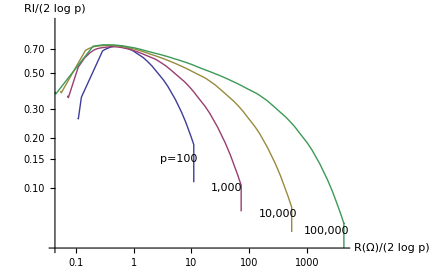

```mathematica
ListLogLogPlot[{ri[100],ri[1000],ri[10000],ri[100000]},
AxesLabel-> {"R(Ω)/(2 log p)","RI/(2 log p)"},
Epilog->{
Text["p=100",Log[{6,0.15}]],
Text["1,000",Log[{40,0.10}]],
Text["10,000",Log[{320,0.07}]],
Text["100,000",Log[{2150,0.055}]]},
Joined->True]
```